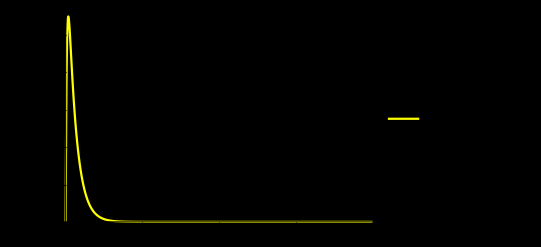

```mathematica
ClearAll["Global*`"];

(* počáteční data součástek *)
Cap= 1;
Res = 1;
uz[t_] := 1;

rovnice = {
0 == iU[t] + iR1[t],
iR1[t] == iC2[t] + iC1[t],
iC1[t] == iR2[t],

u1[t] == uz[t],
u1[t] - u2[t] == Res * iR1[t],
u3[t] == Res * iR2[t],
iC1[t] == Cap * (u2'[t] - u3'[t]),
iC2[t] == Cap * u2'[t],

u2[0] == 0,
u3[0] == 0
};

tmax = 100;

(* Nyní soustavu rovnic vyřešíme - následující řádky jsou Copy-Paste *)

nezname = Union[Cases[rovnice, _Symbol[t], {0, Infinity}]];
reseni = NDSolve[rovnice, nezname, {t, 0, tmax}, StartingStepSize-> 10^-9];

(* Vykreslení grafu - pozor na parametry *)
Plot[{(*u1[t] /. reseni[[1]], u2[t] /. reseni[[1]], *)u3[t] /. reseni[[1]]}, {t, 0, tmax}, PlotStyle -> {Yellow(*, Green, Blue*)}, PlotLegends -> {(*"u1(t)", "u2(t)", *)"u3(t)"}, Background -> Black, PlotRange -> All]
```